```mathematica
M={{a,c},{c,b}}
```

{{a,c},{c,b}}

```mathematica
v={x,y}
```

{x,y}

```mathematica
chi2=1/2  v.M.v
```

1/2 (y (c x+b y)+x (a x+c y))

```mathematica
cx=D[chi2,x]//Simplify
```

a x+c y

```mathematica
Solve[{chi2-R^2==0,cx==0},x]
```

{}

```mathematica
chi2/.x->-c y/a
```

1/2 y (b y-(c^2 y)/a)

```mathematica
1/2 y (b y-(c^2 y)/a)4
```

2 y (b y-(c^2 y)/a)

```mathematica
%//Simplify
```

2 (b-c^2/a) y^2

```mathematica
Solve[%-R^2==0,y]
```

{{y→-R/(√2 √(b-c^2/a))},{y→R/(√2 √(b-c^2/a))}}

```mathematica
cy=D[chi2,y]//Simplify
```

c x+b y

```mathematica
chi2/.y->-c x/b
```

1/2 x (a x-(c^2 x)/b)

```mathematica
%//Simplify
```

1/2 (a-c^2/b) x^2

```mathematica
Solve[%-R^2==0,x]
```

{{x→-(√2 R)/(√(a-c^2/b))},{x→(√2 R)/(√(a-c^2/b))}}

```mathematica
bbEllipse[{x_,y_},a_,b_,c_,R_]:=Module[{xLeft,xRight,yDown,yUp},
yDown=-R/(√(b-c^2/a)); yUp=R/(√(b-c^2/a));
xLeft=-R/(√(a-c^2/b));xRight=R/(√(a-c^2/b));
{FaceForm[],EdgeForm[Thin],Rectangle[{x+xLeft,y+yDown},{x+xRight,y+yUp}]}
]
```

```mathematica
Clear[reconstructEllipse]
```

```mathematica
reconstructEllipse[a_,b_,c_,R_]:=Module[{M,P,ev},M={{a,c},{c,b}}//N;
{ev,P}=Eigensystem[M];

{ev,ArcTan[P[[1,1]],P[[1,2]] ]}]/;NumericQ[a]&&NumericQ[b]&&NumericQ[c] &&NumericQ[R]
```

```mathematica
P=reconstructEllipse[4,4,1,3]
```

{{5.,3.},-0.785398}

```mathematica
ellipse[{x_,y_},{a_,b_},theta_]:=Module[{
R={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}}
},{FaceForm[],EdgeForm[Thick],Polygon[
Table[R.{a Cos[ϕ], b Sin[ϕ]}+{x,y},{ϕ,0,2Pi,0.05}]
]}
]
```

```mathematica
ellipse[{x_,y_},a_,b_,c_,R_]:=Module[{ev,theta},{ev,theta}=reconstructEllipse[ a, b,c,R];
ellipse[{x,y},R{1/Sqrt[ev[[1]] ],1/Sqrt[ev[[2]] ] },theta]
]
```

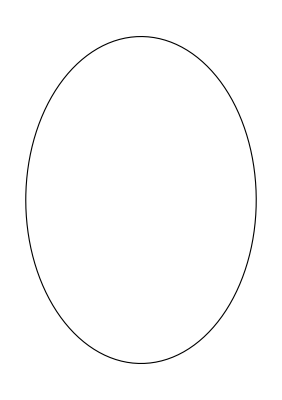

```mathematica
Graphics[ellipse[{0,0},4,2,0,1]]
```

```mathematica
reconstructEllipse[4,2,0,1]
```

{{4.,2.},3.14159}

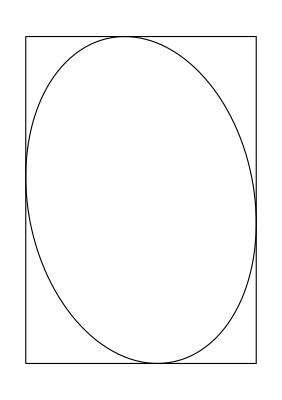

```mathematica
Graphics[{ellipse[{0,0},10,5,1,1],bbEllipse[{0,0},10,5,1,1]}]
```